## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
Get["Cell and Module Library v2.9.m"]
T=298.15;
spec=Get["Z:\\99 home\\02 PhD students\\05 Haohui\\Source & materials\\useful parameters\\spectrum_AM15G"];
```

## Calculate cell output under a particular spectrum and temperature

InGaP/Si tandem cell IV curve

```mathematica
output=iMatchModule$InGaPSi[spec,T,couplingEfficiency->0.5]
```

{{{-0.949643,154.233},{0.600388,152.705},{1.83177,150.797},{1.89754,148.888},{1.92475,146.979},{1.94194,145.07},{1.96443,141.253},{1.97965,137.435},{2.00071,129.8},{2.01572,122.164},{2.03755,106.894},{2.05385,91.6233},{2.07858,61.0822},{2.09781,30.5411},{2.11397,0.}},154.233,2.11397,0.867671,282.898,146.979,1.92475,152.705,219.35}

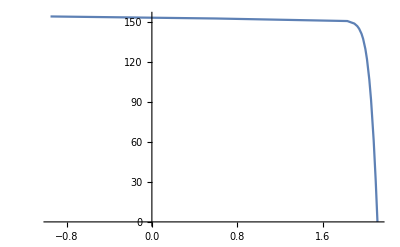

```mathematica
ListLinePlot[output[[1]],PlotRange->Full]
```

GaAs cell with various shunts.

```mathematica
Rsh={100,500,1000,5000,10000}*10^-4;
```

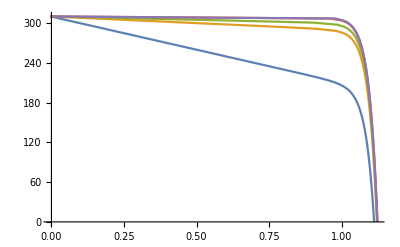

```mathematica
outputs=gaasCell[spec,T,cellParameters->{4*10^-17,2*0.36*Sqrt[4*10^-17],0.1*10^-4,#}]&/@Rsh;
ListLinePlot[outputs[[All,1]],PlotRange->Full]
```

## Investigate the effect of temperature

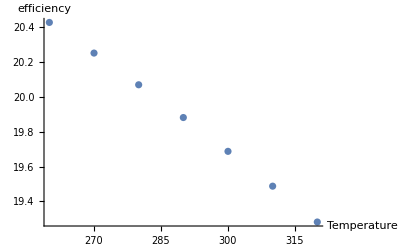

```mathematica
Temp=Range[260,320,10];
eff=Table[ingapCell[spec,t][[5]]/10,{t,Temp}];
ListPlot[{Temp,eff}//Transpose,AxesLabel->{"Temperature","efficiency"}]
```

## Investigate effect of coupling efficiency

{30.8841,30.8994,30.9143,30.9287,30.9427,30.9564,30.9697,30.9826}

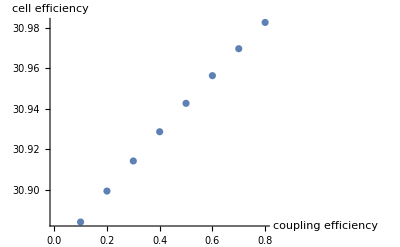

```mathematica
couplingEff=Range[0.1,0.8,0.1];
eff=Table[iMatchModule$GaAsSi[spec,T,couplingEfficiency->eta][[5]]/10,{eta,couplingEff}]
ListPlot[{couplingEff,eff}//Transpose,AxesLabel->{"coupling efficiency","cell efficiency"}]
```